```mathematica
Clear[x,y]
f[x_,y_]=Cos[y]/(x+2)-0.3*y^2
```

-0.3 y^2+Cos[y]/(2+x)

```mathematica
a=0;b=1;h1=0.1;h2=0.05;n1=Floor[(b-a)/h1];n2=Floor[(b-a)/h2];x0=0;y0=0;
```

```mathematica
x0=0;y0=0;
(*а)метод Эйлера Коши*)
eulk1=Table[{x0,y0}={x0+h1,y0+h1/2*(f[x0,y0]+f[x0+h1,y0+h1*f[x0,y0]])},{i,0,n1-1}]
```

{{0.1,0.0487423},{0.2,0.0949711},{0.3,0.138693},{0.4,0.179935},{0.5,0.218739},{0.6,0.255161},{0.7,0.289271},{0.8,0.321145},{0.9,0.350869},{1.,0.378532}}

```mathematica
eulk1//Column
```

{0.1,0.0487423}
{0.2,0.0949711}
{0.3,0.138693}
{0.4,0.179935}
{0.5,0.218739}
{0.6,0.255161}
{0.7,0.289271}
{0.8,0.321145}
{0.9,0.350869}
{1.,0.378532}

```mathematica
eulk1=Prepend[eulk1,{0,0}]
```

{{0,0},{0.1,0.0487423},{0.2,0.0949711},{0.3,0.138693},{0.4,0.179935},{0.5,0.218739},{0.6,0.255161},{0.7,0.289271},{0.8,0.321145},{0.9,0.350869},{1.,0.378532}}

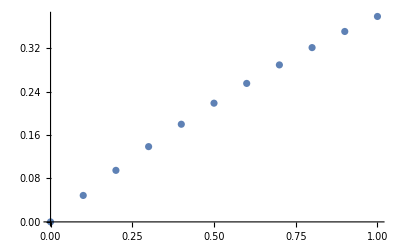

```mathematica
gr1=ListPlot[eulk1]
```

```mathematica
x0=0;y0=0;
eulk2=Table[{x0,y0}={x0+h2,y0+h2/2*(f[x0,y0]+f[x0+h2,y0+h2*f[x0,y0]])},{i,0,n2-1}]
```

{{0.05,0.0246866},{0.1,0.0487458},{0.15,0.0721766},{0.2,0.0949791},{0.25,0.117155},{0.3,0.138707},{0.35,0.159638},{0.4,0.179954},{0.45,0.199661},{0.5,0.218764},{0.55,0.237272},{0.6,0.255193},{0.65,0.272535},{0.7,0.289309},{0.75,0.305523},{0.8,0.321189},{0.85,0.336317},{0.9,0.350919},{0.95,0.365006},{1.,0.378589}}

```mathematica
eulk2=Prepend[eulk2,{0,0}]
```

{{0,0},{0.05,0.0246866},{0.1,0.0487458},{0.15,0.0721766},{0.2,0.0949791},{0.25,0.117155},{0.3,0.138707},{0.35,0.159638},{0.4,0.179954},{0.45,0.199661},{0.5,0.218764},{0.55,0.237272},{0.6,0.255193},{0.65,0.272535},{0.7,0.289309},{0.75,0.305523},{0.8,0.321189},{0.85,0.336317},{0.9,0.350919},{0.95,0.365006},{1.,0.378589}}

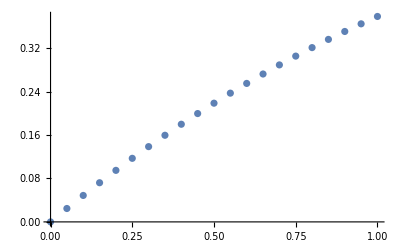

```mathematica
gr2=ListPlot[eulk2]
```

```mathematica
(*б)Метод Рунге-Кутта*)
```

```mathematica
Clear[x,y]
```

```mathematica
f[x_,y_]=Cos[y]/(x+2)-0.3*y^2;
a=0;b=1;x0=0;y0=0;h1=0.1;h2=0.05;n1=Floor[(b-a)/h1];n2=Floor[(b-a)/h2];
```

```mathematica
sol1=List[{x0,y0}];
```

```mathematica
x=x0;y=y0;
For[k=1,k<n1+1,k++,
k1[x_,y_]=h1*f[x,y];
k2[x_,y_]=h1*f[x+h1/2,y+k1[x,y]/2];
k3[x_,y_]=h1*f[x+h1/2,y+k2[x,y]/2];
k4[x_,y_]=h1*f[x+h1,y+k3[x,y]];
x=x+h1;
y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
sol1=Append[sol1,{x,y}]]
```

```mathematica
sol1
```

{{0,0},{0.1,0.0487468},{0.2,0.0949813},{0.3,0.13871},{0.4,0.17996},{0.5,0.218771},{0.6,0.255202},{0.7,0.28932},{0.8,0.321202},{0.9,0.350934},{1.,0.378606}}

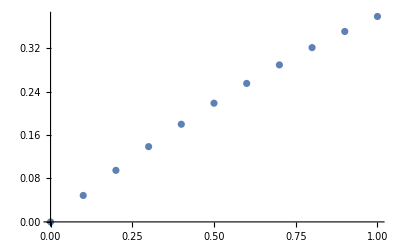

```mathematica
gr3=ListPlot[sol1]
```

```mathematica
Clear[so12]
sol2=List[{x0,y0}];
```

```mathematica
x=x0;y=y0;
For[k=1,k<n2+1,k++,
k1[x_,y_]=h2*f[x,y];
k2[x_,y_]=h2*f[x+h2/2,y+k1[x,y]/2];
k3[x_,y_]=h2*f[x+h2/2,y+k2[x,y]/2];
k4[x_,y_]=h2*f[x+h2,y+k3[x,y]];
x=x+h2;
y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
sol2=Append[sol2,{x,y}]]
```

```mathematica
sol2
```

{{0,0},{0.05,0.024687},{0.1,0.0487468},{0.15,0.0721781},{0.2,0.0949813},{0.25,0.117158},{0.3,0.13871},{0.35,0.159643},{0.4,0.17996},{0.45,0.199667},{0.5,0.218771},{0.55,0.23728},{0.6,0.255202},{0.65,0.272545},{0.7,0.28932},{0.75,0.305535},{0.8,0.321202},{0.85,0.336332},{0.9,0.350934},{0.95,0.365022},{1.,0.378606}}

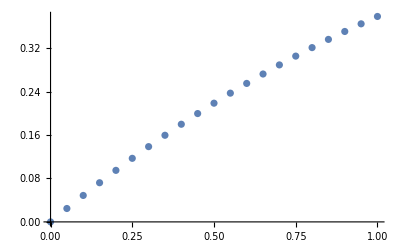

```mathematica
gr4=ListPlot[sol2]
```

```mathematica
Clear[y,x]  (*Очистка предыдущих определений*)
eqn=y'[x]==Cos[y[x]]/(x+2)-0.3*(y[x])^2;
initialCondition=y[0]==0;
solutionDSolve=DSolve[{eqn,initialCondition},y,x];
y1[x_]=y[x]/.Flatten[solutionDSolve]
Print["Аналитическое решение: ",solutionDSolve];
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {DSolve[{y'[x]==Cos[y[«1»]]/Plus[«2»]-0.3 y[«1»]^2,y[0]==0},y,x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

y[x]/.DSolve[{y'[x]==Cos[y[x]]/(2+x)-0.3 y[x]^2,y[0]==0},y,x]

Аналитическое решение: DSolve[{y'[x]==Cos[y[x]]/(2+x)-0.3 y[x]^2,y[0]==0},y,x]

```mathematica
Clear[y,x]  (*Очистка предыдущих определений*)
eqn=y'[x]==Cos[y[x]]/(x+2)-0.3*(y[x])^2;
initialCondition=y[0]==0;
solutionNDSolve=NDSolve[{eqn,initialCondition},y,{x,0,1}]
```

{{y→InterpolatingFunction[…]}}

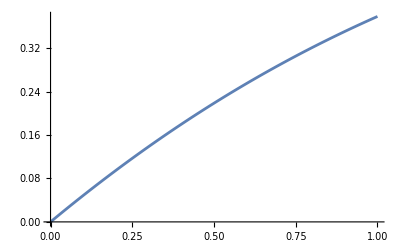

```mathematica
gr5=Plot[Evaluate[y[x]/.solutionNDSolve],{x,0,1}]
```

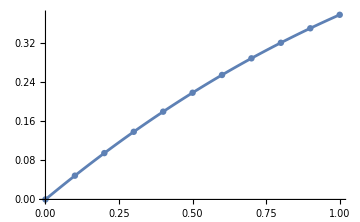

```mathematica
Show[gr1,gr5,ImageSize->Medium]
```

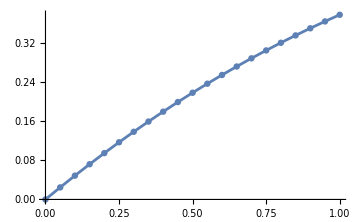

```mathematica
Show[gr2,gr5,ImageSize->Medium]
```

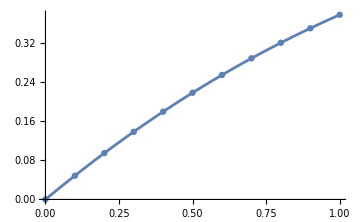

```mathematica
Show[gr3,gr5,ImageSize->Medium]
```

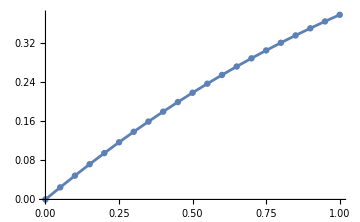

```mathematica
Show[gr4,gr5,ImageSize->Medium]
```